# Algunos Modelos discretos y continuos de Probabilidad

## Principales instrucciones de Mathematica

### Distribuciones discretas

DiscreteUniformDistribution[{i_min,i_max}] representa una distribución uniforme discreta sobre los enteros comprendidos entre imin  y  imax

BernoulliDistribution[p] representa una distribución de Bernoulli de parámetro p

BinomialDistribution[n,p] representa una distribución binomial de parámetros n y p

GeometricDistribution[p] representa una distribución geométrica de parámetro p

NegativeBinomialDistribution[n,p] representa una distribución binomial negativa de parámetros n y p

HypergeometricDistribution[n, D,N] representa una distribución hipergeométrica de parámetros N, D y n

PoissonDistribution[λ] representa una distribución de Poisson de parámetro λ

### Distribuciones continuas

UniformDistribution[{a,b}] representa una distribución uniforme en el intervalo (a, b)

ExponentialDistribution[λ] representa una distribución exponencial de parámetro  λ

NormalDistribution[] representa una distribución normal de media 0 y desviación típica 1, o normal estándar

NormalDistribution[μ, σ] representa una distribución normal de media μ y desviación típica σ

GammaDistribution[α,β]representa una distribución gamma de parámetros α y β

BetaDistribution[α,β]representa una distribución beta de  parámetros  α  y  β

LaplaceDistribution [μ,β] representa una distribución  de Laplace o doble exponencial de media μ y parámetro de escala β

### Características de las distribuciones :

PDF[dist,x]da la función de densidad o distribución de probabilidad (o de masa) de una v.a. con una distribución dist evaluada en x

CDF[dist,x] da la función de distribución de una v.a. con una distribución dist evaluada en x

Manipulate[expr,{u,u_min,u_max}] da un representación interactiva de expr en función de los valores de u, entre u_min y u_max

Nota: Para conseguir el símbolo \[Distributed] debemos escribir \distributed

Mean[dist]  da la esperanza matemática de una v.a. con la distribución dist

Variance[dist] da la varianza de una v.a.  con la distribución dist

```mathematica
StandardDeviation[dist] da la desviación típica o estandar de una v.a. con la distribución dist
```

Moment[dist, r] da el momento de orden r respecto al origen de una v.a. con la distribución dist

Expectation[expr,x\[Distributed]dist] da la esperanza de expr cuando la v.a. x sigue la distribución distr.  Con las funciones adecuadas para  expr  se obtienen los diferentes momentos de la distribución distr

Skewness[dist]  da el coeficiente de asimetría de la distribución dist

## Ejemplo de distribución discreta

Para una v.a. X con una distribución B(10,0.7) calcular:  P(X=1), P(X=0.5), P(1<X<5), P(X>2), la media, la varianza y la desviación típica.

```mathematica
PDF[BinomialDistribution[n,p],x]
```

Piecewise[{{(1-p)^(n-x) p^x Binomial[n,x], 0≤x≤n}, {0, True}}]

```mathematica
(*Binomial[n, x] es el numero combinatorio (n sobre x)*)
```

```mathematica
PDF[BinomialDistribution[10,0.7],k]
```

Piecewise[{{0.3^(10-k) 0.7^k Binomial[10,k], 0≤k≤10}, {0, True}}]

```mathematica
Table[{k,PDF[BinomialDistribution[10,0.7],k]},{k,0,10}]
```

{{0,5.9049×10^-6},{1,0.000137781},{2,0.0014467},{3,0.00900169},{4,0.0367569},{5,0.102919},{6,0.200121},{7,0.266828},{8,0.233474},{9,0.121061},{10,0.0282475}}

```mathematica
(*Par (Valor, Probabilidad que toma en ese valor) Table[{primer miembro, segundo miembro}, {n.bavalores, inicio, fin}]*)
```

P (X = 1)

```mathematica
PDF[BinomialDistribution[10,0.7],1]
```

0.000137781

```mathematica
Binomial[10,1]*.7*.3^9
```

0.000137781

P (X = 0.5)

```mathematica
PDF[BinomialDistribution[10,0.7],0.5]
```

0

P (1< X < 5) = P(X = 2) + P(X = 3) + P(X = 4) = P(X ≤ 4) - P(X ≤ 1) = F(4) - F(1)

```mathematica
PDF[BinomialDistribution[10,0.7],2]+PDF[BinomialDistribution[10,0.7],3]+PDF[BinomialDistribution[10,0.7],4]
```

0.0472053

```mathematica
CDF[BinomialDistribution[10,0.7],4]-CDF[BinomialDistribution[10,0.7],1]
```

0.0472053

P (X > 2) = 1 - P(X ≤ 2) = 1 - F(2)

```mathematica
1-PDF[BinomialDistribution[10,0.7],0]-PDF[BinomialDistribution[10,0.7],1]-PDF[BinomialDistribution[10,.7],2]
```

0.99841

```mathematica
1-CDF[BinomialDistribution[10,0.7],2]
```

0.99841

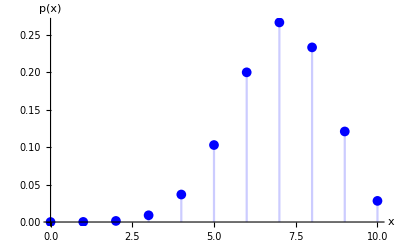

```mathematica
DiscretePlot[PDF[BinomialDistribution[10,0.7],k],{k,0,10},PlotStyle->Blue,PlotMarkers->{Automatic,Medium}, AxesLabel->{"x","p(x)"}]
```

```mathematica
Manipulate[DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,0,n},PlotMarkers->{Automatic,Medium},PlotStyle->Blue,Filling->None, AxesLabel->{"x","p(x)"}],{n,1,20,1},{p,0,1}]
```

E(X) = np = 7                   var(X) = npq = 2.1             σ = +√2.1= 1.449

```mathematica
Mean[BinomialDistribution[10,0.7]]
```

7.

```mathematica
Variance[BinomialDistribution[10,0.7]]
```

2.1

```mathematica
StandardDeviation[BinomialDistribution[10,0.7]]
```

1.44914

```mathematica
N[PDF[PoissonDistribution[30],0]]
(*El N es para que aparezca de forma numerica (practica 1)*)
```

9.35762×10^-14

## Ejemplo de distribución continua

Para una v.a. X con una distribución Exp(3) calcular:  P(1<X<3), P(X>2), la media, la varianza, la desviación típica y el coeficiente de simetría

```mathematica
PDF[ExponentialDistribution[3],x]
```

Piecewise[{{3 ⅇ^(-3 x), x≥0}, {0, True}}]

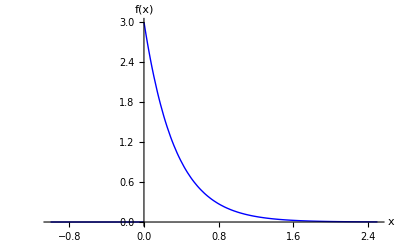

```mathematica
Plot[PDF[ExponentialDistribution[3],x],{x,-1,2.5},PlotRange->All,PlotStyle->{Blue,Thick},AxesLabel->{"x", "f(x)"}]
```

P (1< X < 3) = ∫_1^3 3 ⅇ^(-3 x)ⅆx = F(3) - F(1)

```mathematica
∫_1^3 3. ⅇ^(-3 x)ⅆx
```

```mathematica
Exp[-3.]-Exp[-9]
```

0.0496637

```mathematica
CDF[ExponentialDistribution[3],3.]-CDF[ExponentialDistribution[3],1]
```

0.0496637

P (X > 2)

```mathematica
∫_2^∞ 3. ⅇ^(-3 x)ⅆx
```

```mathematica
1-CDF[ExponentialDistribution[3],2.]
```

E(X) = 1/λ = 1/3                   var(X) = 1/λ^2 = 1/9                σ =  1/λ = 1/3                 γ = 2

```mathematica
Mean[ExponentialDistribution[3]]
```

1/3

```mathematica
Variance[ExponentialDistribution[3]]
```

1/9

```mathematica
StandardDeviation[ExponentialDistribution[3]]
```

1/3

```mathematica
Skewness[ExponentialDistribution[3]]
```

2

```mathematica
Manipulate[Plot[PDF[ExponentialDistribution[λ],x],{x,-2,20},PlotRange->{{-2,15},{0,2}},PlotStyle->{Purple, Thick},AxesLabel->{"x","f(x)"}],{λ,.1,2}]
```

La distribución Normal

```mathematica
PDF[NormalDistribution[μ,σ],x]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

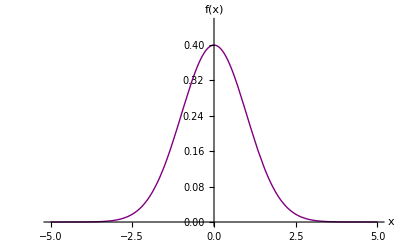

```mathematica
Plot[PDF[NormalDistribution[0,1],x],{x,-5,5},PlotRange->{{-5,5},{0,0.45}},PlotStyle->{Purple, Thick},AxesLabel->{"x","f(x)"}]
```

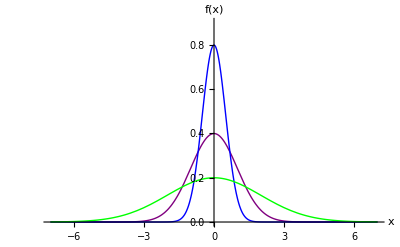

```mathematica
Plot[{PDF[NormalDistribution[0,1],x],PDF[NormalDistribution[0,0.5],x] ,PDF[NormalDistribution[0,2],x]},{x,-7,7},PlotRange->{{-7,7},{0,0.9}},PlotStyle->{{Purple,Thick},{Blue,Thick},{ Green, Thick}},AxesLabel->{"x","f(x)"}]
```

```mathematica
InverseCDF[NormalDistribution[4,6],0.5]
```

4.

```mathematica
(*Esto me da un percentil. Cual es el valor cuya funcion de distribucion me da 0.5*)
```

```mathematica
Quantile[NormalDistribution[], 0.6915]
```

0.500107

Ejemplo: La resistencia a la tensión del papel empleado para hacer bolsas para víveres que fabrica una empresa papelera es una variable aleatoria que sigue una distribución normal cuyos valores (medidos en kg/cm^3) varían desde 2.24 hasta 3.36.

a) Calcular los parámetros, media y desviación típica, y dibujar la gráfica de la función de densidad de la distribución normal anterior indicando la posición de la media.
b) Se elige una bolsa al azar con una resistencia superior a 2.7 kg/cm^3. ¿Cuál es la probabilidad de que tenga una resistencia superior a 2.7kg/cm^3 e inferior a 3 kg/cm^3?
c) El fabricante garantiza que devolverá el dinero a todo aquel que compre una bolsa cuya resistencia sea inferior a un valor k. Determinar el valor de k de modo que tenga que devolver el dinero como máximo al 15% de los compradores.
d) Uno de los compradores de estas bolsas requiere que su resistencia sea de , al menos, 2.6824 kg/cm^3. Si se elige un paquete de 6 bolsas, cuál es la probabilidad de que al menos 5 de las bolsas del paquete cumplan con las exigencias del comprador?

La variable aleatoria que definimos para los  apartados a) , b) y c) será X=”resistencia del papel empleado para hacer bolsas”. X~N(m,s)

a) Cálculo de m y s

```mathematica
Solve[m-4*s==2.24&& m+4*s==3.36, {m,s}]
```

{{m→2.8,s→0.14}}

b) Se elige una bolsa al azar con una resistencia superior a 2.7 kg/cm^3. ¿Cuál es la probabilidad de que tenga una resistencia superior a 2.7 kg/cm^3 e inferior a 3 kg/cm^3?

```mathematica
P(2.7<X<3|X>2.7)=0.899585
```

```mathematica
P(X>2.7)=1-P(X≤2.7)
```

```mathematica
1-CDF[NormalDistribution[2.8,0.14],2.7]
```

```mathematica
P(2.7<X<3)=F(3)-F(2.7)
```

```mathematica
CDF[NormalDistribution[2.8,0.14],3]-CDF[NormalDistribution[2.8,0.14],2.7]
```

Función de densidad

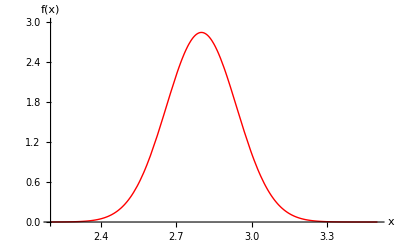

```mathematica
Plot[PDF[NormalDistribution[2.8,0.14],x],{x,2.2,3.5},PlotRange->{{2.2,3.5},{0,3}},PlotStyle->{Red, Thick},AxesLabel->{"x","f(x)"}]
```

c)  El fabricante garantiza que devolverá el dinero a todo aquel que compre una bolsa cuya resistencia sea inferior a un valor k. Determinar el valor de k de modo que tenga que devolver el dinero como máximo al 15% de los compradores.
Nota: Es el cálculo de un cuantil

```mathematica
InverseCDF[NormalDistribution[2.8, 0.14], 0.15]
```

2.6549

d) Uno de los compradores de estas bolsas requiere que su resistencia sea de , al menos, 2.6824 kg/cm^3. Si se elige un paquete de 6 bolsas, ¿cuál es la probabilidad de que al menos 5 de las bolsas del paquete cumplan con las exigencias del comprador?
Definimos la variable aleatoria N=” Número de bolsas que cumplen las exigencias del comprador en un paquete de 6”
N∼Bi(n=6, p), donde p=P(X>2.6824)

P (X > 2.6824) = 1 - P (X <= 2.6824)

```mathematica
1-CDF[NormalDistribution[2.8, 0.14], 2.6824]
```

0.799546

La probabilidad pedida es P(N≥5)=1-P(N<5)=1-P(N≤4)

```mathematica
1-CDF[BinomialDistribution[6, 0.799546],4]
```

0.654244

La distribución Gamma

```mathematica
PDF[GammaDistribution[α,β],x]
```

Piecewise[{{(ⅇ^(-x/β) x^(-1+α) β^-α)/Gamma[α], x>0}, {0, True}}]

Obsérvese que según la parametrización dada en clase, α = p y a = 1/β

```mathematica
Manipulate[Plot[PDF[GammaDistribution[α,β],x],{x,-2,20},PlotRange->{{-2,20},{0,2}},PlotStyle->{Purple, Thick},AxesLabel->{"x","f(x)"}],{α,.1,1},{β,0.1,20}]
```

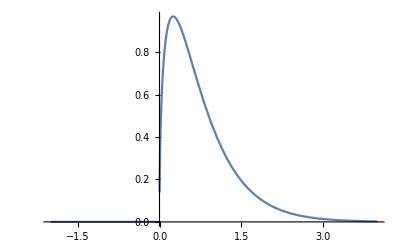

```mathematica
Plot[PDF[GammaDistribution[1.5, 1/2], x], {x, -2, 4}, PlotRange->All]
```

```mathematica
(*Ga(a=2, p=1,5), alpha = p = 1,5, a=1/beta = 2, beta = 1/2*)
```

```mathematica
Mean[GammaDistribution[α,β]]
```

α β

```mathematica
Mean[GammaDistribution[p,1/a]]
```

p/a

```mathematica
Variance[GammaDistribution[p,1/a]]
```

p/a^2

El parámetro 1/a  (β) es un  parámetro de escala de la distribución. 
El parámetro p es una parámetro de forma

La distribución Beta

```mathematica
PDF[BetaDistribution[α,β],x]
```

Piecewise[{{((1-x)^(-1+β) x^(-1+α))/Beta[α,β], 0<x<1}, {0, True}}]

```mathematica
Manipulate[Plot[PDF[BetaDistribution[α,β],x],{x,0,1},PlotRange->{{0,1},{0,5}},PlotStyle->{Purple, Thick},AxesLabel->{"x","f(x)"}],{α,.1,1},{β,0.1,5}]
```

```mathematica
Mean[BetaDistribution[a, b]]
```

a/(a+b)

```mathematica
Variance[BetaDistribution[a, b]]
```

(a b)/((a+b)^2 (1+a+b))

```mathematica
Expectation[Exp[t*x], x \[Distributed] BetaDistribution[a, b]]
```

Hypergeometric1F1[a,a+b,t]